```mathematica
Manipulate[
Module[{list},
SeedRandom[reset];
list=RandomSample[{"A","B","C"}];

Graphics[{
{EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{1,1}]},
Text[Style[list[[1]],20],{0.1,0.1}],Text[Style[list[[2]],20],{0.5,0.5}],Text[Style[list[[3]],20],{0.9,0.9}]
},ImageSize->{600,400},AspectRatio->Full]
],
Grid@{{Button[" new problem ",reset++],Control[{reset,None}]}}
]
```

```mathematica
Manipulate[
Module[{},
SeedRandom[reset];
RandomSample[{"A","B","C"}]
],
Grid@{{Button[" new problem ",reset++],Control[{reset,None}]}}
]
```

```mathematica
Manipulate[
Module[{list},
SeedRandom[reset];
list=RandomSample[{"A","B","C"}];

Graphics[{Thick,
{EdgeForm@Thick,FaceForm@None,Rectangle[{-1,0},{1,2}]},
{Blue,Line[{#,-#^2+0.75}&/@Range[-1,1,0.1]],Text[Style["A",17,Blue,Background->White],{0,0.75}]},
{Red,Line[{#,-#^2+1.25}&/@Range[-1,1,0.1]],Text[Style["B",17,Red,Background->White],{0,1.25}]},
{Green,Line[{#,-#^2+1.75}&/@Range[-1,1,0.1]],Text[Style["C",17,Green,Background->White],{0,1.75}]}
},ImageSize->{600,400},AspectRatio->Full,PlotRange->{-0.01,2}]
],
Grid@{{Button[" new problem ",reset++],Control[{reset,None}]}}
]
```

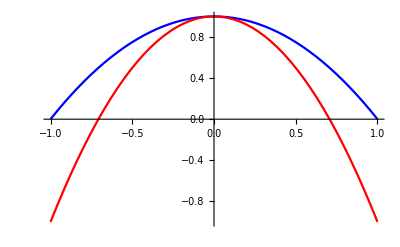

```mathematica
Plot[{-x^2+1,-2*x^2+1},{x,-1,1},PlotStyle->{Blue,Red}]
```